```mathematica
(*Area calc*)
```

```mathematica
Cross[{(xc-xa),(yc-ya),(zc-za)},{(xb-xa),(yb-ya),(zb-za)}]
```

{yb za-yc za-ya zb+yc zb+ya zc-yb zc,-xb za+xc za+xa zb-xc zb-xa zc+xb zc,xb ya-xc ya-xa yb+xc yb+xa yc-xb yc}

```mathematica
1/2(√((yb za-yc za-ya zb+yc zb+ya zc-yb zc)^2+(-xb za+xc za+xa zb-xc zb-xa zc+xb zc)^2+(xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)^2))
```

1/2 √((xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)^2+(-xb za+xc za+xa zb-xc zb-xa zc+xb zc)^2+(yb za-yc za-ya zb+yc zb+ya zc-yb zc)^2)

```mathematica
D[1/2 √((xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)^2+(-xb za+xc za+xa zb-xc zb-xa zc+xb zc)^2+(yb za-yc za-ya zb+yc zb+ya zc-yb zc)^2),xa]
```

(2 (-yb+yc) (xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)+2 (zb-zc) (-xb za+xc za+xa zb-xc zb-xa zc+xb zc))/(4 √((xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)^2+(-xb za+xc za+xa zb-xc zb-xa zc+xb zc)^2+(yb za-yc za-ya zb+yc zb+ya zc-yb zc)^2))

```mathematica
D[1/2 √((xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)^2+(-xb za+xc za+xa zb-xc zb-xa zc+xb zc)^2+(yb za-yc za-ya zb+yc zb+ya zc-yb zc)^2),xc]
```

(2 (-ya+yb) (xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)+2 (za-zb) (-xb za+xc za+xa zb-xc zb-xa zc+xb zc))/(4 √((xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)^2+(-xb za+xc za+xa zb-xc zb-xa zc+xb zc)^2+(yb za-yc za-ya zb+yc zb+ya zc-yb zc)^2))

```mathematica
D[(2Pi-F[x])^2/G[x]^2,x]
```

-(2 (2 π-F[x]) F'[x])/G[x]^2-(2 (2 π-F[x])^2 G'[x])/G[x]^3

```mathematica
(*if a triangle contains node i: *)
```

```mathematica
dαdri[{xm_,ym_,zm_},{xk_,yk_,zk_},{xii_,yii_,zii_}]:={D[ArcCos[((xi-xk)*(xm-xk)+(yi-yk)*(ym-yk)+(zi-zk)*(zm-zk))/(√((xi-xk)^2+(yi-yk)^2+(zi-zk)^2)√((xm-xk)^2+(ym-yk)^2+(zm-zk)^2))],xi]/.{xi->xii,yi->yii,zi->zii},D[ArcCos[((xi-xk)*(xm-xk)+(yi-yk)*(ym-yk)+(zi-zk)*(zm-zk))/(√((xi-xk)^2+(yi-yk)^2+(zi-zk)^2)√((xm-xk)^2+(ym-yk)^2+(zm-zk)^2))],yi]/.{xi->xii,yi->yii,zi->zii},D[ArcCos[((xi-xk)*(xm-xk)+(yi-yk)*(ym-yk)+(zi-zk)*(zm-zk))/(√((xi-xk)^2+(yi-yk)^2+(zi-zk)^2)√((xm-xk)^2+(ym-yk)^2+(zm-zk)^2))],zi]/.{xi->xii,yi->yii,zi->zii}};
```

```mathematica
((-xk+xm)/(rki*rkm)-((xi-xk) (cos[Subscript[α, k]]))/rki)/(√(1-(cos^2)[Subscript[α, k]]));
```

```mathematica
D[ArcCos[((xn-xi)*(xm-xi)+(yn-yi)*(ym-yi)+(zn-zi)*(zm-zi))/(√((xn-xi)^2+(yn-yi)^2+(zn-zi)^2)√((xm-xi)^2+(ym-yi)^2+(zm-zi)^2))],zi]
```

-(((-zi+zn) ((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn)))/(√((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) ((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)^(3/2))+(2 zi-zm-zn)/(√((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) √((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2))+((-zi+zm) ((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn)))/(((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2)^(3/2) √((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)))/(√(1-((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn))^2/(((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) ((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2))))

```mathematica
-(((-xi+xn) cos[Subscript[α, k]])/rin^2+(2 xi-xm-xn)/(rin*rim)+((-xi+xm) cos[Subscript[α, k]])/rim^2)/(√(1-(cos^2)[Subscript[α, k]]));
```

```mathematica
D[ArcCos[((xc-xa)*(xb-xa)+(yc-ya)*(yb-ya)+(zc-za)*(zb-za))/(√((xc-xa)^2+(yc-ya)^2+(zc-za)^2)√((xb-xa)^2+(yb-ya)^2+(zb-za)^2))],xa]
```

-(((-xa+xc) ((-xa+xb) (-xa+xc)+(-ya+yb) (-ya+yc)+(-za+zb) (-za+zc)))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa+xc)^2+(-ya+yc)^2+(-za+zc)^2)^(3/2))+(2 xa-xb-xc)/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa+xc)^2+(-ya+yc)^2+(-za+zc)^2))+((-xa+xb) ((-xa+xb) (-xa+xc)+(-ya+yb) (-ya+yc)+(-za+zb) (-za+zc)))/(((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2)^(3/2) √((-xa+xc)^2+(-ya+yc)^2+(-za+zc)^2)))/(√(1-((-xa+xb) (-xa+xc)+(-ya+yb) (-ya+yc)+(-za+zb) (-za+zc))^2/(((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa+xc)^2+(-ya+yc)^2+(-za+zc)^2))))

```mathematica
D[ArcCos[((xc-xa)*(xb-xa)+(yc-ya)*(yb-ya)+(zc-za)*(zb-za))/(√((xc-xa)^2+(yc-ya)^2+(zc-za)^2)√((xb-xa)^2+(yb-ya)^2+(zb-za)^2))],xc]
```

-(-((-xa+xc) ((-xa+xb) (-xa+xc)+(-ya+yb) (-ya+yc)+(-za+zb) (-za+zc)))/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa+xc)^2+(-ya+yc)^2+(-za+zc)^2)^(3/2))+(-xa+xb)/(√((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) √((-xa+xc)^2+(-ya+yc)^2+(-za+zc)^2)))/(√(1-((-xa+xb) (-xa+xc)+(-ya+yb) (-ya+yc)+(-za+zb) (-za+zc))^2/(((-xa+xb)^2+(-ya+yb)^2+(-za+zb)^2) ((-xa+xc)^2+(-ya+yc)^2+(-za+zc)^2))))

```mathematica
dαkdri[{xm_,ym_,zm_},{xk_,yk_,zk_},{xi_,yi_,zi_}]:={-(((-xk+xm)/(√((xi-xk)^2+(yi-yk)^2+(zi-zk)^2) √((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2))-((xi-xk) ((xi-xk) (-xk+xm)+(yi-yk) (-yk+ym)+(zi-zk) (-zk+zm)))/(((xi-xk)^2+(yi-yk)^2+(zi-zk)^2)^(3/2) √((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2)))/(√(1-((xi-xk) (-xk+xm)+(yi-yk) (-yk+ym)+(zi-zk) (-zk+zm))^2/(((xi-xk)^2+(yi-yk)^2+(zi-zk)^2) ((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2))))),-(((-yk+ym)/(√((xi-xk)^2+(yi-yk)^2+(zi-zk)^2) √((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2))-((yi-yk) ((xi-xk) (-xk+xm)+(yi-yk) (-yk+ym)+(zi-zk) (-zk+zm)))/(((xi-xk)^2+(yi-yk)^2+(zi-zk)^2)^(3/2) √((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2)))/(√(1-((xi-xk) (-xk+xm)+(yi-yk) (-yk+ym)+(zi-zk) (-zk+zm))^2/(((xi-xk)^2+(yi-yk)^2+(zi-zk)^2) ((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2))))),-(((-zk+zm)/(√((xi-xk)^2+(yi-yk)^2+(zi-zk)^2) √((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2))-((zi-zk) ((xi-xk) (-xk+xm)+(yi-yk) (-yk+ym)+(zi-zk) (-zk+zm)))/(((xi-xk)^2+(yi-yk)^2+(zi-zk)^2)^(3/2) √((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2)))/(√(1-((xi-xk) (-xk+xm)+(yi-yk) (-yk+ym)+(zi-zk) (-zk+zm))^2/(((xi-xk)^2+(yi-yk)^2+(zi-zk)^2) ((-xk+xm)^2+(-yk+ym)^2+(-zk+zm)^2)))))}
```

```mathematica
dαidri[{xm_,ym_,zm_},{xi_,yi_,zi_},{xn_,yn_,zn_}]:={-((((-xi+xn) ((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn)))/(√((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) ((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)^(3/2))+(2 xi-xm-xn)/(√((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) √((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2))+((-xi+xm) ((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn)))/(((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2)^(3/2) √((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)))/(√(1-((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn))^2/(((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) ((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2))))), -((((-yi+yn) ((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn)))/(√((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) ((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)^(3/2))+(2 yi-ym-yn)/(√((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) √((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2))+((-yi+ym) ((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn)))/(((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2)^(3/2) √((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)))/(√(1-((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn))^2/(((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) ((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2))))),-((((-zi+zn) ((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn)))/(√((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) ((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)^(3/2))+(2 zi-zm-zn)/(√((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) √((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2))+((-zi+zm) ((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn)))/(((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2)^(3/2) √((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)))/(√(1-((-xi+xm) (-xi+xn)+(-yi+ym) (-yi+yn)+(-zi+zm) (-zi+zn))^2/(((-xi+xm)^2+(-yi+ym)^2+(-zi+zm)^2) ((-xi+xn)^2+(-yi+yn)^2+(-zi+zn)^2)))))}
```

```mathematica
(*Spherical*)
```

```mathematica
v1={0,0,0.01};
```

```mathematica
v2={1,0,0};
```

```mathematica
v3={1/2,(√3)/2,0};
```

```mathematica
v4={-1/2,(√3)/2,0};
```

```mathematica
v5={-1,0,0};
```

```mathematica
v6={-1/2,(-√3)/2,0};
```

```mathematica
v7={1/2,(-√3)/2,0};
```

```mathematica
v8={2,0,0};
```

```mathematica
v9={3/2,(√3)/2,0};
```

```mathematica
v10={1,√3,0};
```

```mathematica
v11={0,√3,0};
```

```mathematica
v12={-1,√3,0};
```

```mathematica
v13={-3/2,(√3)/2,0};
```

```mathematica
v14={-2,0,0};
```

```mathematica
v15={-3/2,(-√3)/2,0};
```

```mathematica
v16={-1,-√3,0};
```

```mathematica
v17={0,-√3,0};
```

```mathematica
v18={1,-√3,0};
```

```mathematica
v19={3/2,(-√3)/2,0};
```

```mathematica
angleSum1 = ArcCos[Dot[v2-v1,v3-v1]/(√Dot[v2-v1,v2-v1] √Dot[v3-v1,v3-v1])]+ArcCos[Dot[v3-v1,v4-v1]/(√Dot[v4-v1,v4-v1] √Dot[v3-v1,v3-v1])]+ArcCos[Dot[v4-v1,v5-v1]/(√Dot[v4-v1,v4-v1] √Dot[v5-v1,v5-v1])]+ArcCos[Dot[v5-v1,v6-v1]/(√Dot[v5-v1,v5-v1] √Dot[v6-v1,v6-v1])]+ArcCos[Dot[v6-v1,v7-v1]/(√Dot[v6-v1,v6-v1] √Dot[v7-v1,v7-v1])]+ArcCos[Dot[v7-v1,v2-v1]/(√Dot[v7-v1,v7-v1] √Dot[v2-v1,v2-v1])];
```

```mathematica
angleSum2=ArcCos[Dot[v8-v2,v9-v2]/(√Dot[v8-v2,v8-v2] √Dot[v9-v2,v9-v2])]+ArcCos[Dot[v3-v2,v9-v2]/(√Dot[v3-v2,v3-v2] √Dot[v9-v2,v9-v2])]+ArcCos[Dot[v3-v2,v1-v2]/(√Dot[v3-v2,v3-v2] √Dot[v1-v2,v1-v2])]+ArcCos[Dot[v7-v2,v1-v2]/(√Dot[v7-v2,v7-v2] √Dot[v1-v2,v1-v2])]+ArcCos[Dot[v7-v2,v19-v2]/(√Dot[v7-v2,v7-v2] √Dot[v19-v2,v19-v2])]+ArcCos[Dot[v8-v2,v19-v2]/(√Dot[v8-v2,v8-v2] √Dot[v19-v2,v19-v2])];
```

```mathematica
angleSum3=ArcCos[Dot[v9-v3,v10-v3]/(√Dot[v9-v3,v9-v3] √Dot[v10-v3,v10-v3])]+ArcCos[Dot[v11-v3,v10-v3]/(√Dot[v11-v3,v11-v3] √Dot[v10-v3,v10-v3])]+ArcCos[Dot[v11-v3,v4-v3]/(√Dot[v11-v3,v11-v3] √Dot[v4-v3,v4-v3])]+ArcCos[Dot[v1-v3,v4-v3]/(√Dot[v1-v3,v1-v3] √Dot[v4-v3,v4-v3])]+ArcCos[Dot[v1-v3,v2-v3]/(√Dot[v1-v3,v1-v3] √Dot[v2-v3,v2-v3])]+ArcCos[Dot[v9-v3,v2-v3]/(√Dot[v9-v3,v9-v3] √Dot[v2-v3,v2-v3])];
```

```mathematica
angleSum4=angleSum3;
```

```mathematica
angleSum5=angleSum3;
```

```mathematica
angleSum6=angleSum3;
```

```mathematica
angleSum7=angleSum3;
```

```mathematica
FuncForPotentail[x_,a_]:= (2 π-x)^(a-1.0)
```

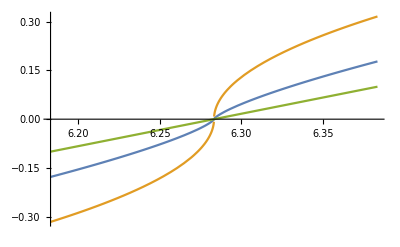

```mathematica
Plot[{Sign[(x-2Pi)](Abs[(x-2Pi)])^0.75,Sign[(x-2Pi)]Sqrt[Abs[(x-2Pi)]],(x-2Pi)},{x,2Pi-0.1,2Pi+0.1}]
```

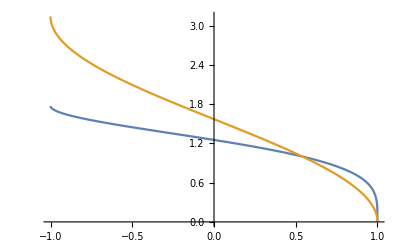

```mathematica
Plot[{Sign[ArcCos[x]] √Abs[ArcCos[x]],ArcCos[x]},{x,-1,1}]
```

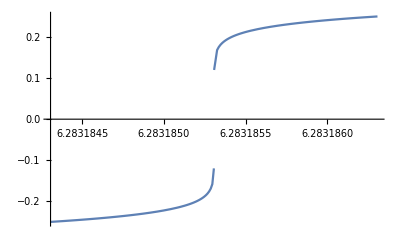

```mathematica
Plot[{Sign[(x-2Pi)](Abs[(x-2Pi)])^0.1},{x,2Pi-0.000001,2Pi+0.000001}]
```

```mathematica
Integrate[1/(1+Exp[-a(F[x]-2Pi)])-1/2,x]
```

∫(-1/2+1/(1+ⅇ^(-a (-2 π+F[x]))))ⅆx

```mathematica
α =2.0;
β = 100;
```

```mathematica
grad1Total = β* α*(FuncForPotentail[angleSum1,α]*(dαidri[v2,v1,v3]+dαidri[v3,v1,v4]+dαidri[v4,v1,v5]+dαidri[v5,v1,v6]+dαidri[v6,v1,v7]+dαidri[v7,v1,v2])+
FuncForPotentail[angleSum2,α]*(dαkdri[v3,v2,v1]+dαkdri[v7,v2,v1])+
FuncForPotentail[angleSum7,α]*(dαkdri[v6,v7,v1]+dαkdri[v2,v7,v1])+
FuncForPotentail[angleSum3,α]*(dαkdri[v2,v3,v1]+dαkdri[v4,v3,v1])+
FuncForPotentail[angleSum4,α]*(dαkdri[v5,v4,v1]+dαkdri[v3,v4,v1])+
FuncForPotentail[angleSum5,α]*(dαkdri[v6,v5,v1]+dαkdri[v4,v5,v1])+
FuncForPotentail[angleSum6,α]*(dαkdri[v5,v6,v1]+dαkdri[v7,v6,v1]))//N
```

{0.,0.,-0.0047988}

```mathematica
(dαidri[v2,v1,v3]+dαidri[v3,v1,v4]+dαidri[v4,v1,v5]+dαidri[v5,v1,v6]+dαidri[v6,v1,v7]+dαidri[v7,v1,v2])
```

{0.,0.,-0.0692705}

```mathematica
angleSum1
```

6.28284

```mathematica
Sqrt[1.03^2-1]
```

0.246779

```mathematica
(dαkdri[v3,v2,v1]+dαkdri[v7,v2,v1])
```

{0.000115451,0.,0.0115451}

```mathematica
(dαkdri[v6,v7,v1]+dαkdri[v2,v7,v1])
```

{0.0000577254,-0.0000999833,0.0115451}

```mathematica
(dαkdri[v2,v3,v1]+dαkdri[v4,v3,v1])
```

{0.0000577254,0.0000999833,0.0115451}

```mathematica
(dαkdri[v5,v4,v1]+dαkdri[v3,v4,v1])
```

{-0.0000577254,0.0000999833,0.0115451}

```mathematica
(dαkdri[v6,v5,v1]+dαkdri[v4,v5,v1])
```

{-0.000115451,0.,0.0115451}

```mathematica
(dαkdri[v5,v6,v1]+dαkdri[v7,v6,v1])
```

{-0.0000577254,-0.0000999833,0.0115451}

```mathematica
dαkdri[v7,v6,v1]
```

{-0.865997,0.499917,0.00577254}

```mathematica
dαkdri[v5,v6,v1]
```

{0.865939,-0.500017,0.00577254}

```mathematica
(*Hyperbolic*)
```

```mathematica
v1={0,0,0.0};
```

```mathematica
v2={1,0,0.25};
```

```mathematica
v3={1/2,(√3)/2,0};
```

```mathematica
v4={-1/2,(√3)/2,0};
```

```mathematica
v5={-1,0,0};
```

```mathematica
v6={-1/2,(-√3)/2,0};
```

```mathematica
v7={1/2,(-√3)/2,0};
```

```mathematica
v8={2,0,0};
```

```mathematica
v9={3/2,(√3)/2,0};
```

```mathematica
v10={1,√3,0};
```

```mathematica
v11={0,√3,0};
```

```mathematica
v12={-1,√3,0};
```

```mathematica
v13={-3/2,(√3)/2,0};
```

```mathematica
v14={-2,0,0};
```

```mathematica
v15={-3/2,(-√3)/2,0};
```

```mathematica
v16={-1,-√3,0};
```

```mathematica
v17={0,-√3,0};
```

```mathematica
v18={1,-√3,0};
```

```mathematica
v19={3/2,(-√3)/2,0};
```

```mathematica
angleSum1 = ArcCos[Dot[v2-v1,v3-v1]/(√Dot[v2-v1,v2-v1] √Dot[v3-v1,v3-v1])]+ArcCos[Dot[v3-v1,v4-v1]/(√Dot[v4-v1,v4-v1] √Dot[v3-v1,v3-v1])]+ArcCos[Dot[v4-v1,v5-v1]/(√Dot[v4-v1,v4-v1] √Dot[v5-v1,v5-v1])]+ArcCos[Dot[v5-v1,v6-v1]/(√Dot[v5-v1,v5-v1] √Dot[v6-v1,v6-v1])]+ArcCos[Dot[v6-v1,v7-v1]/(√Dot[v6-v1,v6-v1] √Dot[v7-v1,v7-v1])]+ArcCos[Dot[v7-v1,v2-v1]/(√Dot[v7-v1,v7-v1] √Dot[v2-v1,v2-v1])]
```

6.31749

```mathematica
angleSum2=ArcCos[Dot[v8-v2,v9-v2]/(√Dot[v8-v2,v8-v2] √Dot[v9-v2,v9-v2])]+ArcCos[Dot[v3-v2,v9-v2]/(√Dot[v3-v2,v3-v2] √Dot[v9-v2,v9-v2])]+ArcCos[Dot[v3-v2,v1-v2]/(√Dot[v3-v2,v3-v2] √Dot[v1-v2,v1-v2])]+ArcCos[Dot[v7-v2,v1-v2]/(√Dot[v7-v2,v7-v2] √Dot[v1-v2,v1-v2])]+ArcCos[Dot[v7-v2,v19-v2]/(√Dot[v7-v2,v7-v2] √Dot[v19-v2,v19-v2])]+ArcCos[Dot[v8-v2,v19-v2]/(√Dot[v8-v2,v8-v2] √Dot[v19-v2,v19-v2])]
```

6.07734

```mathematica
angleSum3=ArcCos[Dot[v9-v3,v10-v3]/(√Dot[v9-v3,v9-v3] √Dot[v10-v3,v10-v3])]+ArcCos[Dot[v11-v3,v10-v3]/(√Dot[v11-v3,v11-v3] √Dot[v10-v3,v10-v3])]+ArcCos[Dot[v11-v3,v4-v3]/(√Dot[v11-v3,v11-v3] √Dot[v4-v3,v4-v3])]+ArcCos[Dot[v1-v3,v4-v3]/(√Dot[v1-v3,v1-v3] √Dot[v4-v3,v4-v3])]+ArcCos[Dot[v1-v3,v2-v3]/(√Dot[v1-v3,v1-v3] √Dot[v2-v3,v2-v3])]+ArcCos[Dot[v9-v3,v2-v3]/(√Dot[v9-v3,v9-v3] √Dot[v2-v3,v2-v3])]
```

6.31749

```mathematica
angleSum4=ArcCos[Dot[v3-v4,v11-v4]/(√Dot[v3-v4,v3-v4] √Dot[v11-v4,v11-v4])]+ArcCos[Dot[v11-v4,v12-v4]/(√Dot[v11-v4,v11-v4] √Dot[v12-v4,v12-v4])]+ArcCos[Dot[v12-v4,v13-v4]/(√Dot[v12-v4,v12-v4] √Dot[v13-v4,v13-v4])]+ArcCos[Dot[v13-v4,v5-v4]/(√Dot[v13-v4,v13-v4] √Dot[v5-v4,v5-v4])]+ArcCos[Dot[v5-v4,v1-v4]/(√Dot[v5-v4,v5-v4] √Dot[v1-v4,v1-v4])]+ArcCos[Dot[v1-v4,v3-v4]/(√Dot[v1-v4,v1-v4] √Dot[v3-v4,v3-v4])]
```

6.28319

```mathematica
angleSum5=angleSum4;
```

```mathematica
angleSum6=angleSum4;
```

```mathematica
angleSum7=angleSum3;
```

```mathematica
α =2.0;
β = 1;
```

```mathematica
grad1Total = β* α*(FuncForPotentail[angleSum1,α]*(dαidri[v2,v1,v3]+dαidri[v3,v1,v4]+dαidri[v4,v1,v5]+dαidri[v5,v1,v6]+dαidri[v6,v1,v7]+dαidri[v7,v1,v2])+
FuncForPotentail[angleSum2,α]*(dαkdri[v3,v2,v1]+dαkdri[v7,v2,v1])+
FuncForPotentail[angleSum7,α]*(dαkdri[v6,v7,v1]+dαkdri[v2,v7,v1])+
FuncForPotentail[angleSum3,α]*(dαkdri[v2,v3,v1]+dαkdri[v4,v3,v1])+
FuncForPotentail[angleSum4,α]*(dαkdri[v5,v4,v1]+dαkdri[v3,v4,v1])+
FuncForPotentail[angleSum5,α]*(dαkdri[v6,v5,v1]+dαkdri[v4,v5,v1])+
FuncForPotentail[angleSum6,α]*(dαkdri[v5,v6,v1]+dαkdri[v7,v6,v1]))//N
```

{-0.0313448,0.,0.125379}